```mathematica
games={1,3,5,7};

single64={{0.82,31.62,54.97},
{0.81,24.08,41.15},
{0.77,19.42,31.19},
{0.73,16.26,25.57}};

double64={{0.83,29.56,47.05},
{0.76,21.61,31.56},
{0.72,17.97,24.74},
{0.68,15.81,21.14}};

doubleext64={{0.81,28.70,47.21},
{0.75,20.42,30.15},
{0.71,16.68,23.35},
{0.67,14.45,19.09}};

roundrobin64={{0.60,14.60,17.83},
{0.53,11.45,13.23},
{0.50,10.11,11.54},
{0.47,9.16,10.42}};
```

```mathematica
data={single64,double64,doubleext64,roundrobin64};
```

```mathematica
datat=Transpose/@data;
```

```mathematica
<<"PlotLegends`"
```

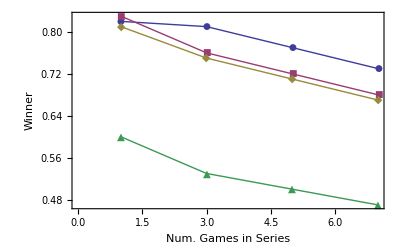

```mathematica
ListLinePlot[({games,#[[1]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","Winner"},Frame->{{True,False},{True,False}},Axes->False,PlotMarkers->Automatic]
```

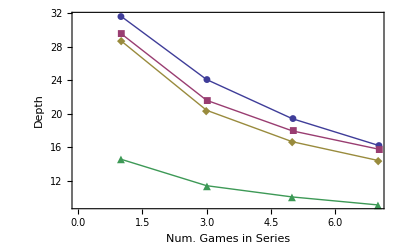

```mathematica
ListLinePlot[({games,#[[2]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","Depth"},Frame->{{True,False},{True,False}},Axes->False,PlotMarkers->Automatic]
```

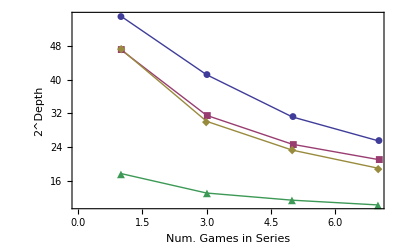

```mathematica
ListLinePlot[({games,#[[3]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","2^Depth"},Frame->{{True,False},{True,False}},Axes->False,PlotMarkers->Automatic]
```

```mathematica
playerdata={{
{0.64,3.10,4.04},
{0.89,7.93,12.78},
{0.87,18.46,36.56},
{0.97,36.47,82.26},
{0.98,67.28,166.50},
{0.95,110.56,267.79},
{0.94,151.36,343.18},
{0.94,193.35,463.83}
},
{
{0.61,3.11,3.86},
{0.77,7.81,12.10},
{0.94,18.63,37.07},
{0.97,35.44,78.82},
{0.94,63.68,150.85},
{0.94,102.33,226.71},
{0.95,138.10,288.71},
{0.94,178.28,366.62}
},
{
{0.61,3.13,3.93},
{0.82,7.83,12.34},
{0.95,18.09,35.75},
{0.93,35.49,79.34},
{0.91,63.65,146.26},
{0.91,102.33,232.98},
{0.92,135.98,292.12},
{0.94,166.37,354.15}
}};
```

```mathematica
playerdatat=Transpose/@playerdata;
```

```mathematica
players={4,8,16,32,64,128,256,512};
```

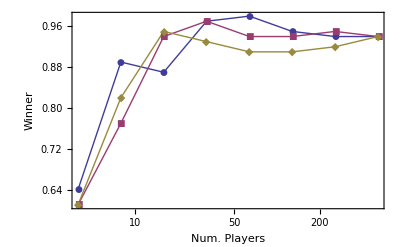

```mathematica
ListLogLinearPlot[({players,#[[1]]}//Transpose)&/@playerdatat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Players","Winner"},Frame->{{True,False},{True,False}},Axes->False,Joined->True,PlotMarkers->Automatic]
```

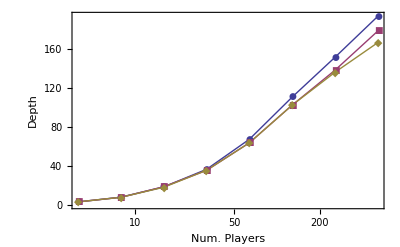

```mathematica
ListLogLinearPlot[({players,#[[2]]}//Transpose)&/@playerdatat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Players","Depth"},Frame->{{True,False},{True,False}},Axes->False,Joined->True,PlotMarkers->Automatic]
```

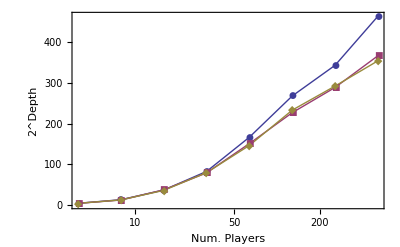

```mathematica
ListLogLinearPlot[({players,#[[3]]}//Transpose)&/@playerdatat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Players","2^Depth"},Frame->{{True,False},{True,False}},Axes->False,Joined->True,PlotMarkers->Automatic]
```